```mathematica
intensTrue=Import[NotebookDirectory[]<>"intensity.dat"];intensTrue=Partition[intensTrue,Length[intensTrue[[1]]]];Dimensions[intensTrue]
```

{91,91,91}

```mathematica
intensRecon=Import[NotebookDirectory[]<>"finish_intensity.dat"];intensRecon=Partition[intensRecon,Length[intensRecon[[1]]]];Dimensions[intensRecon]
```

{91,91,91}

```mathematica
qmax=(Length[intensTrue]-1)/2
```

45

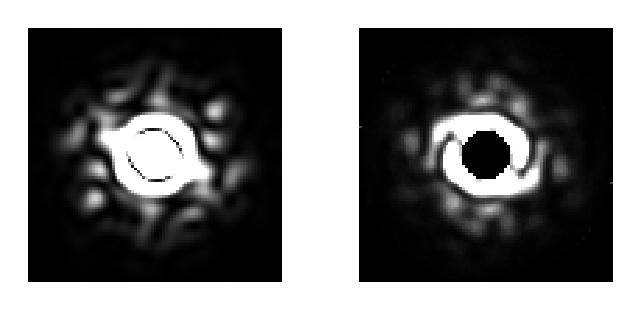

```mathematica
GraphicsArray[{Graphics[Raster[500intensTrue[[qmax+1]]]],Graphics[Raster[500intensRecon[[qmax+1]]]]}]
```

```mathematica
eps=Union[Flatten[(intensRecon[[qmax+1]]/.{-1.->0.})]][[2]]
```

1.30107×10^-8

```mathematica
logIntens=Log[(intensRecon[[qmax+1]]/.{-1.->eps,0.->eps})];
{maxLog,minLog}={Max[logIntens],Min[logIntens]}
```

{-4.1909,-18.1575}

```mathematica
Graphics[Raster[(logIntens-minLog)/(maxLog-minLog),ColorFunction->(If[#==0.,Black,Hue[#]]&)]]
```

-Graphics-